# 1. Gravity Tunnel in the Earth

## 1.1 Densities definition

### 1.1.1 Effective density function

First, we define the value of the constants that we are going to use: Acceleration of gravity, radius of the Earth, mean density of the Earth and gravity constant:

```mathematica
g=9.8156;  (*m/s2*)  
R=6.371 10^6; (*m*) 
ρ0 = 5513 ; (*kg/m3*)
G = 6.67 10^(-11) ;(* N m2/kg^2*)
```

We want to build a function of the following form

```mathematica
ρ1(r; b, c, d)= Subscript[ρ, 0] b (1-c r/R)^d
```

being b,c,d parameters to determine. It can be written in the code as the function

```mathematica
ρ 1[r_,b_,c_,d_]:=ρ0 b Power[1-c r/R,d]
```

this density have the following forms

```mathematica
Manipulate[Plot[ρ 1[r,b,c,d],{r,0,R},PlotStyle-> RGBColor[b,c,d]],{b,0.2,4,0.2},{c,0.1,1,0.1},{d,0.1,1,0.1}]
```

#### 1.1.1.1 Effective density functions from PREM

Now, we have the next conditions to determine parameters b,c,d:

Density in the center of the Earth: ρ(0)=ρ_0 b =13088.5

then

```mathematica
b = 13088.5/ρ0 ;
Print["b = ", b]
```

b = 2.37325

Density at the surface must be that of the water (1000kg/m^2):  ρ(r = R) = b ρ_0(1-c )^d = ρ_R

then

```mathematica
(1-c)^d=0.1813/2.37325 = 0.076393
```

The third conditions is given from the total mass, we must have

```mathematica
Subscript[M, T] = 4π ∫_0^R ρ(r)r^2 ⅆr = 4π Subscript[ρ, 0] b∫_0^R (1 - c r/R)^d r^2 ⅆr
```

Doing the integral in Mathematica gives the analytical expression

```mathematica
Clear[b,R]
 Integrate[b*x^2*(1-c*(x/R))^d,{x,0,R}]
```

ConditionalExpression[(b (2+(1-c)^d (-1+c) (2+c (1+d) (2+c (2+d)))) R^3)/(c^3 (1+d) (2+d) (3+d)), Re[c]≤1||c∉ℝ]

so we can express the third condition as:

```mathematica
7.1197*(2-(1-x)^(y+1)(2+2x(1+y)+x^2(2+3y+y^2)))/(x^3*(6+11*y+6*y^2+y^3))-1
```

3 b [ 2 -  (1-c)^(d+1)(2+2c(1+d)+c^2(2+3d + d^2))]=  c^3(6 + 11d + 6 d^2+ d^3)

To solve the system of equations (1) and (3), this would be the code on Mathematica to solve the system, but it takes too long

```mathematica
Remove[x,y];
NSolve[{(1-x)^y==0.0763,7.1197(2-(1-x)^(y+1)*(2+2*x*(1+y)+x^2*(2+3*y+x^2)))/(x^3*(6+11*y+6*y^2+y^3))==1},{x,y}]
```

On the other hand, the next code on Python finds the answer in a few seconds:

from scipy.optimize import root

def equations(p):
	x, y  = p
	eq1 = (1-x)**y - 0.0763
	eq2 = 7.12*(2 - (1 - x)**(y + 1)*(2 + 2*x*(1 + y) + x**2*(2 + 3*y + y**2))) / (x**3*(6 + 11*y + 6*y**2 + y**3)) - 1
	return ( eq1 , eq2 )
	
sol =  root(equations, (0.1, 0.1), method='lm', jac=None, tol=None, callback=None, options={'col_deriv': 0, 'xtol': 1.49012e-08, 'ftol': 1.49012e-08, 'gtol': 0.0, 'maxiter': 0, 'eps': 0.0, 'factor': 100, 'diag': None})


x = sol.x[0]
y = sol.x[1]

#print(equations((x, y)))
print('x = ', x)
print('y = ', y)

x = 0.9875151202043234
y = 0.5867499795022912

For simplicity, the density function to work from here on is then

```mathematica
b = 2.37325;
c = 0.9875151202043234;
d = 0.5867499795022912;
ρ[r_]:=ρ 1[r,b,c,d]
```

Plotting with this result gives

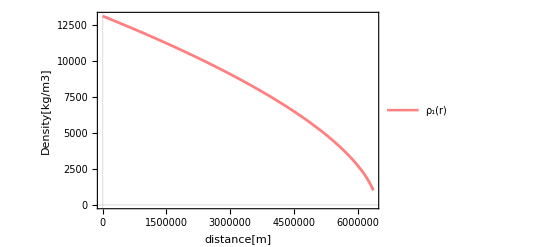

```mathematica
EffctiveFunction=Plot[{ρ[x]},{x,0,R},
PlotLegends->Placed[{"ρ_1(r)"},{Right,Top}],
PlotStyle->{Thickness[0.005],Pink},
Frame->True,
FrameLabel->{{"Density[kg/m3]",None},{"distance[m]",None}},
PlotTheme->"Scientific"]
```

#### 1.1.1.2 Numerical density from PREM

Now, let’s import PREM data and plot to see how this distribution looks like

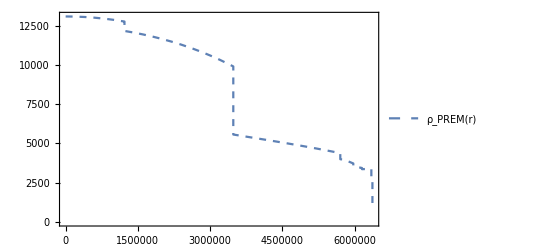

```mathematica
data=Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/prem-density.csv","Table"];
density prem=ListLinePlot[data,
PlotLegends->Placed[{"ρ_PREM(r)"},{Right,Top}],
PlotStyle->Dashed,
Frame->True]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/density_prem.pdf",density prem];
```

To compare, we can plot them together

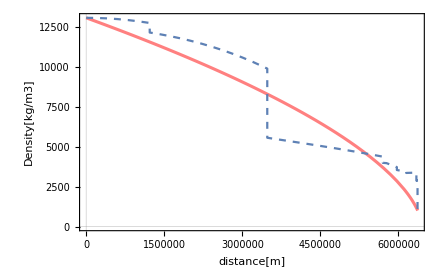

```mathematica
densities = Show[EffctiveFunction,density prem]
```

we see that actually the proposed functions fit between the data.

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/1-densities.pdf",densities];
```

### 1.1.2 Numerical Checks for the Effective Density Function

#### 1.1.2.1 Masses

Now, we want to determine the mass as a function of the radius. At r=R we would like to have M(r) = M ~ 6 x 10^15,

```mathematica
M[r_]:= 4 π  NIntegrate[ρ[x] x^2,{x,0,r}]
```

the output at the radius is

```mathematica
Print[Style["M_T = ",20],Style[M[R],20], Style[" kg",20,Italic]]
```

M_T = 5.97237×10^24 kg

the expected one.  To see the behaviour at any other point let’s plot this functions

```mathematica
Masses = Plot[{M[r]},{r,0,R},
PlotStyle->{{Thickness[0.008],Pink}},
Frame->True,
FrameLabel->{{"M(r) [kg]",None},{"r [m]",None}}]
```

-Graphics-

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/2-masses.pdf",Masses];
```

#### 1.1.2 Gravity

From density functions, we can compute it as

```mathematica
a(r) = (4π G)/r^2∫_0^r ρ(r')r'^2 ⅆr'
```

As this is the same integral of the mass, we have already compute analytically with Mathematica,  ‘til any point r, this gives

```mathematica
Clear[b,c,d,R]
Integrate[x^2*(1-c*(x/R))^d,{x,0,r}]
```

ConditionalExpression[(2 R^3+(1-(c r)/R)^d (c r-R) (c^2 (1+d) (2+d) r^2+2 c (1+d) r R+2 R^2))/(c^3 (1+d) (2+d) (3+d)), ]

Now, let’s define the function as

```mathematica
a analytic [r_]:= 3 g b (2 R^2-(1-c r/R)^(d+1)(c^2(1+d)(2+d)r^2 + 2c(1+d)r R + 2 R^2))/(c^3r^2(6 + 11d + 6 d^2+ d^3))
```

At the  radius the gravity is

```mathematica
Print[Style["g_analytic = ",20],Style[a analytic[R],20], Style[" m/s^2",20,Italic]]
```

g_analytic = 9.81567 m/s^2

As it should be. In terms of the binomial theorem, this can be made also analytically as

```mathematica
a (r) = (4π G)/r^2 Subscript[ρ, 0] b∫_0^r (1- c r'/R)^d r'^2 ⅆr' = (4π G)/r^2 (3M)/(4π R^3)∑_(n=0)^∞ ({{d}, {n}})(-c)^n/R^n∫_0^r r^(n+2)ⅆr
	= 3 g b  ∑_(n=0)^∞ ({{d}, {n}})(-c)^n/(n+3) (r/R)^(n+1)
```

in the code

```mathematica
a[r_]:=3 b g Sum[QBinomial[d,n,1] (-c)^n(r/R)^(n+1)/(n+3),{n,0,Infinity}]
```

at the surface we have

```mathematica
Print[Style["g_Binom = ",20],Style[a[R],20], Style[" m/s^2",20,Italic]]
```

g = 9.81667 m/s^2

which is a little above the expected value. 
We can both functions in the hole range by making plots

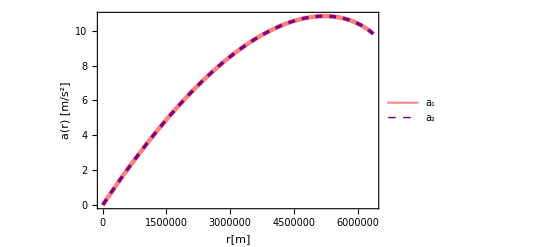

```mathematica
AccelerationFunctions=Plot[{a analytic[r],a[r]},{r,0,R},
PlotLegends->Placed[{"a_1","a_2"},{Right,Bottom}],
PlotStyle->{{Thickness[0.008],Pink},{Purple,Thickness[0.006],Dashed}},
Frame->True,
FrameLabel->{{"a(r) [m/s^2]",None},{"r[m]",None}}]
```

We see now that they are indeed the same.

#### From Prem

Here we write the official data in the pertinent units and interpolate it to have a continuous function

```mathematica
gravity prem = Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/gravity_prem.csv","Table"];
g prem=Interpolation[gravity prem,InterpolationOrder->5]
gravity prem ad = Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/prem-grav-ad.csv","Table"];
g prem ad=Interpolation[gravity prem ad,InterpolationOrder->5]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

Now, we can plot the three functions together

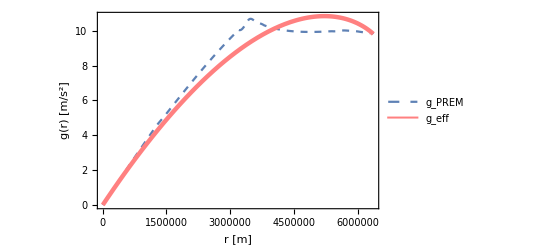

```mathematica
accelerations = Plot[{g prem[r],a[r]},{r,0,R},
PlotLegends->Placed[{"g_PREM","g_eff"},{Right,Bottom}],
PlotStyle->{Dashed,{Thickness[0.008],Pink}},
Frame->True,
FrameLabel->{{"g(r) [m/s^2]",None},{"r [m]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/3-accelerations.pdf",accelerations];
```

## 1.2 Numerical Predictions

### 1.2.1 Velocity Profiles

Next, we are going to compute the velocities of the already found density profiles, in principle this should be made according to

```mathematica
v(r)=√(8π G ∫_r^R ∫_0^y ρ(x)x^2 ⅆx 1/y^2 ⅆy)
```

or in terms of the integral of the acceleration.  For the PREM profile, we have

```mathematica
vprem[r_?NumberQ] :=Sqrt[2*NIntegrate[g prem[x],{x,r,R}]]
vprem ad[r_?NumberQ] := Sqrt[2/3*NIntegrate[ g prem ad[x], {x, r, 1}]]
```

For the case of the effective density function, this will be the direct integration of the analytical acceleration

```mathematica
v analytic [r_]:= Sqrt[8 Pi G ρ0  NIntegrate[ b Power[1-c x /R,d]  x^2 /y^2,{y,r,R},{x,0,y}]]
```

while this is an still analytical expression using the binomial theorem expression:

```mathematica
v ad[r_]:=Sqrt[2 b Sum[QBinomial[d,k,1]*(-c)^k  (1 - r^(k+2))/((k+2)(k+3)),{k,0,20}]]
v[r_]:=Sqrt[8 Pi G ρ0 R^2]Sqrt[ b Sum[QBinomial[d,k,1]*(-c)^k  (1 - r^(k+2))/((k+2)(k+3)),{k,0,10}]]
```

We can see that they exactly the same and very close to the value predicted by PREM distribution

```mathematica
Print[Style["v_PREM (0)= ", 20],Style[vprem[0],20],Style[" m/s", 20, Italic]," , ", 
Style["v_analytic (0)= ", 20],Style[v analytic[0],20],Style[" m/s", 20, Italic]," , ",
Style["v_Binom (0)= ", 20],Style[v[0],20],Style[" m/s", 20, Italic]]
```

v_PREM (0)= 9914.72 m/s , v_analytic (0)= 9840.17 m/s , v_Binom (0)= 9840.17 m/s

In the hole range, the distribution of velocities looks as

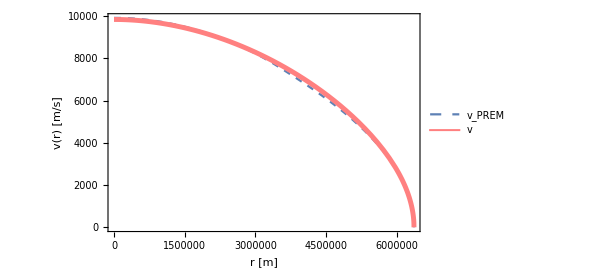

```mathematica
velocities = Plot[{vprem[x],v analytic[x]},{x,0,R},
PlotLegends->Placed[{"v_PREM","v"},{Right,Top}],
PlotStyle->{{ColorData[97][1],Dashed},{Thickness[0.008],Pink}},
Frame->True,
FrameLabel->{{"v(r) [m/s]",None},{"r [m]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/4-velocities.pdf",velocities];
```

### 1.2.2 Times chord path

We have arrived to the most important part of this work, the prediction of the traversal time of the train through the chord path. In the case between antipodes, the times are given by

```mathematica
T= 2∫_0^R 1/(v(r))ⅆr.
```

in a more general chord path, characterized by a parameter d (distance from the polar axis), they are

```mathematica
T(d)= 2∫_d^R r/(v(r))1/(√(r^2-d^2))ⅆr.
```

With the velocity profiles founded above, we can define three functions for computing times; one for PREM case and two for the effective density function. The reason for having taken all this time the two methods is that analytic  functions were faster to plot above, but the integration of binomial case in this case results better, so we will define them but keep from here on, only the second case

```mathematica
Tprem[d_]:= NIntegrate[x/(vprem[x]*Sqrt[x^2 - d^2 ]),{x,d,R}]
Tprem ad[d_]:= NIntegrate[x/(vprem ad[x]*Sqrt[x^2 - d^2 ]),{x,d,1}]
T1[d_]:= NIntegrate[x/(v analytic[x]*Sqrt[x^2 - d^2 ]),{x,d,R}]
T ad[d_]:= NIntegrate[x/(v ad[x]*Sqrt[x^2 - d^2 ]),{x,d,1}]
T[d_]:= R NIntegrate[x/(v[x]*Sqrt[x^2 - d^2 ]),{x,d,1}]
```

Now, we can compute the output of this functions in minutes:

```mathematica
Print[ Style["T_PREM =",20],Style[Tprem[0]/30,20],Style[" min",20, Italic],
"  ,  ",Style["T_Eff =",20],Style[T[0]/30,20],Style[" min",20, Italic]]
```

T_PREM =38.1878 min  ,  T_Eff =37.7624 min

this means an error of

```mathematica
Print[ Style["Error = ",20], Style[(Tprem[0]-T[0])/Tprem[0]*100,20], Style[" %",20]]
```

Error = 1.11406 %

But, again, the best way to compare the results is with a plot

```mathematica
ListTimesPrem=Table[{d,Tprem ad[d]*Sqrt[1/3* R/g]/30},{d,0,0.95,0.05}]
ListTimesEff=Table[{x,T ad[x]*Sqrt[1/3* R/g]/30},{x,0.,0.95,0.05}]
```

{{0.,38.1875},{0.05,38.199},{0.1,38.2335},{0.15,38.2912},{0.2,38.3723},{0.25,38.4768},{0.3,38.6057},{0.35,38.7602},{0.4,38.9416},{0.45,39.1509},{0.5,39.3874},{0.55,39.6464},{0.6,39.9084},{0.65,40.1663},{0.7,40.423},{0.75,40.6812},{0.8,40.9447},{0.85,41.2192},{0.9,41.5137},{0.95,41.827}}

{{0.,37.7288},{0.05,37.7383},{0.1,37.7667},{0.15,37.8138},{0.2,37.8791},{0.25,37.9626},{0.3,38.0644},{0.35,38.1844},{0.4,38.3233},{0.45,38.4814},{0.5,38.6596},{0.55,38.859},{0.6,39.0811},{0.65,39.3276},{0.7,39.6009},{0.75,39.9041},{0.8,40.241},{0.85,40.6169},{0.9,41.0388},{0.95,41.5165}}

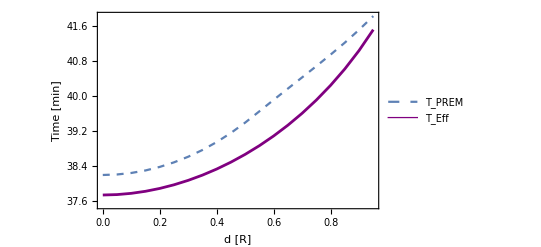

```mathematica
chordtimes = ListLinePlot[{ListTimesPrem, ListTimesEff},
PlotLegends->Placed[{"T_PREM","T_Eff"},{Left,Top}],
PlotStyle->{{ColorData[97][1],Dashed},{Purple,Thickness[0.005]}},
Frame->True,
FrameLabel->{{"Time [min]",None},{"d [R]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/5-chordtimes.pdf",chordtimes];
```

## 1.3 Further Analysis of the Gravity Tunnel

### 1.3.1 Shape of the brachistochrone curves

The other important part of this work is the time for the path of fastest descent and its shape. To find it we will need to perform the following integration of the trajectory:

```mathematica
θ(r) = ∫_d^r I(x,d)ⅆx
```

with the integrand

```mathematica
I(r,d)=[r^4/d^2((v(d))/(v(r)))^2- r^2]^(-1/2)
```

The next is the code to define auxiliary functions for the integration,

```mathematica
I1[x_,d_]:=1/(Sqrt[x^4/d^2 *(v ad[d]/v ad[x])^2-x^2] )
I prem[x_,d_]:=1/(Sqrt[x^4/d^2 *(vprem ad[d]/vprem ad[x])^2-x^2] )
```

With them we can proceed to do the integration in a valid range

```mathematica
θ [r_?NumericQ,d_?NumericQ]:=If[r>d,NIntegrate[I1[x,d],{x,d,r}],0.0]
θ prem [r_?NumericQ,d_?NumericQ]:=Piecewise[{{0.0, r≤ d},{NIntegrate[I prem[x,d],{x,d,r}],r>d}}]
(*If[r>d,NIntegrate[I prem[x,d],{x,d,r}],0.0]*)
```

In order to plot the trajectories and visualise the motion in a better way, we should make a polar plot. As this is not so immediate, even in Mathematica, we have to make some lists with the data points, which is what the next cell does

```mathematica
Step = 0.02;
Theta3=Table[{θ[i,0.3],i},{i,0.3,1,Step}];
Theta3 minus=Table[{- θ[i,0.3],i},{i,0.3,1,Step}];
Theta6=Table[{θ[i,0.6],i},{i,0.6,1,Step}];
Theta6 minus=Table[{- θ[i,0.6],i},{i,0.6,1,Step}];
ThetaPrem3=Table[{θ prem[i,0.3],i},{i,0.3,1,Step}];
ThetaPrem3 minus=Table[{- θ prem[i,0.3],i},{i,0.3,1,Step}];
ThetaPrem6=Table[{θ prem[i,0.6],i},{i,0.6,1,Step}];
ThetaPrem6 minus=Table[{- θ prem[i,0.6],i},{i,0.6,1,Step}];
```

With that data, we plot the Earth as the Black circle, and the trajectories inside it.

```mathematica
Circ = PolarPlot[1,{t,0,2 Pi},PlotStyle->{Thick,Black},Frame->True,FrameTicks->None,Axes->None];
```

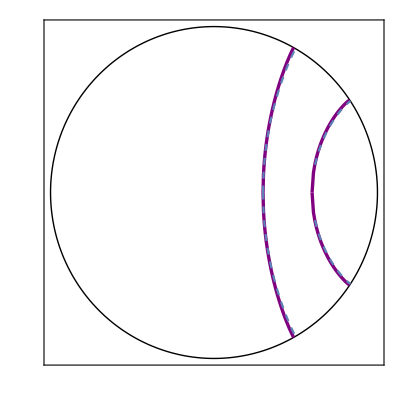

```mathematica
Trajectories =ListPolarPlot[{Theta3,Theta3 minus,Theta6,Theta6 minus},Joined->True, 
PlotStyle->{{Purple,Thickness[0.006]}},Frame->True,FrameTicks->None,Axes->None];
TrajectoriesPrem =ListPolarPlot[{ThetaPrem3,ThetaPrem3 minus,ThetaPrem6,ThetaPrem6 minus},Joined->True, 
PlotStyle->{{ColorData[97][1],Dashed}},Frame->True,FrameTicks->None,Axes->None];
Brachistochornes = Show[Circ,Trajectories,TrajectoriesPrem ]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/6-braqShapes.pdf",Brachistochornes];
```

### 1.3.2 Times for the brachistochrone curves

In this subsection we are going to find the times for the brachistochrone paths plotted above. As this are by definition the paths of fastest descent, the times should be the minimal times. The formula to compute this times is better given by

```mathematica
Subscript[T, BRAQ]= ∫_d^r (√(1+x^2 ω^2(x)))/(v(x))ⅆx
```

Where  ω(r)=∂_r θ(r,d). As  θ itself is an integral, by the fundamental theorem of calculus, ω = I(r,d):

```mathematica
ω[r_, d_]:=I1[r,d]
ω prem[r_, d_]:=I prem[r,d]
```

and  then the times for a given maximum approaching point d

```mathematica
Tbraq[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 ω[r,d]^2]/v ad[r],{r,d,1}]
Tbraq prem[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 ω prem[r,d]^2]/vprem ad[r],{r,d,1}]
```

let’s check that the times taken when d=0 are the same as for the chord path

```mathematica
Print[ Style["T_PREM^BRAQ =",20],Style[Tbraq prem[0]Sqrt[1/3* R/g]/30,20],Style[" min",20, Italic],
"  ,  ",Style["T_Eff^BRAQ =",20],Style[Tbraq[0]Sqrt[1/3* R/g]/30,20],Style[" min",20, Italic]]
```

T_PREM^BRAQ =38.1875 min  ,  T_Eff^BRAQ =37.7288 min

They are almost the same, maybe it’s a question of precision, but we can trust in this results. We can see the complete dependence of the times on the position of the tunnel in the following plot

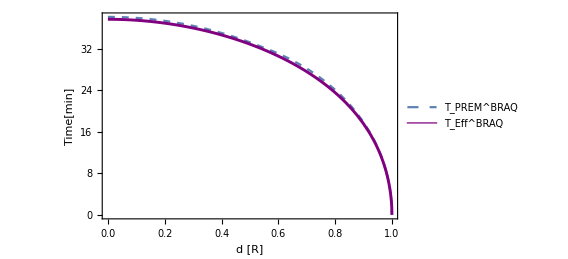

```mathematica
BraqTimes = Plot[{Tbraq prem[x]Sqrt[1/3* R/g]/30, Tbraq[x]Sqrt[1/3* R/g]/30},{ x,0,1},
PlotLegends->Placed[{"T_PREM^BRAQ","T_Eff^BRAQ"},{Left,Bottom}],
PlotStyle->{{ColorData[97][1],Dashed},{Purple,Thickness[0.005]}},
Frame->True,
FrameLabel->{{"Time[min]",None},{"d [R]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/7-braqTimes.pdf",BraqTimes];
```

### 1.3.2 Accelerations

In this last section, we want give a dynamical reason for the difference between chord path times and brachistochrone path times. First, define some auxiliary functions

```mathematica
dist[d_]:=Sqrt[1-(Sin[θ[1,d]])^2]
dist prem[d_]:=Sqrt[1-(Sin[θ prem[1,d]])^2]
```

with the radial accelerations and the these auxiliary functions we can define the acceleration in the direction of motion for the chord path

```mathematica
a chord[r_,d_]:=Re[a analytic[r R]/g Sqrt[r^2-(dist[d])^2]/r]
a prem chord[x_,d_]:=Re[g prem ad[x]*Sqrt[x^2-(dist prem[d])^2]/x]
```

as well as the acceleration in the direction of motion for the brachistochrone paths

```mathematica
a braq[x_,d_]:=Re[a analytic[x R]/g *Sin[θ[x, d]]]
a braq prem[x_,d_]:=Re[g prem ad[x]*Sin[θ prem[x, d]]]
```

Now, let’s plot

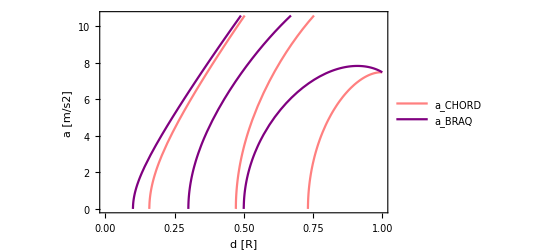

```mathematica
Accelerations chord braq =Plot[{Table[9.81*a chord[x,d],{d,0.1,0.5,0.2}],Table[9.81*a braq[x,d],{d,0.1,0.5,0.2}]},{x,0,1},
PlotRange->{0.0001,10.6},
PlotLegends->Placed[{"a_CHORD","a_BRAQ"},{Left,Top}],
PlotStyle->{Pink,Purple},
Frame->True,
FrameLabel->{{"a [m/s2]",None},{"d [R]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/8-Acceleration-chord-braq.pdf",Accelerations chord braq];
```

Author: Nicolás Gómez Cruz